129.28828729416733318

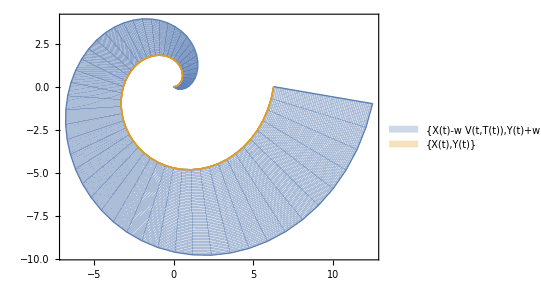

```mathematica
X[t_]:=t Cos[t];
Y[t_]:=t Sin[t];
H[t_]:=0;
G[t_]:=-t;
T[t_]:=0;

u[t_] := X'[t]/Sqrt[Factor[X'[t]^2+Y'[t]^2]];
v[t_] := Y'[t]/Sqrt[Factor[X'[t]^2+Y'[t]^2]];
U[t_,T_]:= u[t]Cos[T]-v[t]Sin[T];
V[t_,T_]:= v[t]Cos[T]+u[t]Sin[T];

NIntegrate[Sqrt[(X'[t]-w D[V[t,T[t]],t])^2+(Y'[t]+w D[U[t,T[t]],t])^2],{t, 0,2 Pi}, {w,G[t], H[t]}, WorkingPrecision->20]
ParametricPlot[{{X[t]-w V[t,T[t]],Y[t]+w U[t,T[t]]},{ X[t], Y[t]}}, {t, 0, 2 Pi}, {w, G[t], H[t]}, PlotLegends->"Expressions"] 
Animate[ParametricPlot[{X[t]-w V[t,T[t]]G[t],Y[t]+w U[t,T[t]] G[t]}, {t, 0, 2Pi},PlotRange -> {{-8, 14}, {-11, 6}}], {w, 0,1}]
```

```mathematica
Table[D[y[t],{t,i}],{i,0,5}]/.Derivative[n_][y][t]->n
```

{y[t],1,2,3,4,5}